```mathematica
(* Van egy függvény, azt kiterjesztjük úgy, hogy páros/páratlan legyen: *)
ClearAll[fun,funOrig]
funOrig[x_]=x^2-x;
fun[x_]=(x/(2π))^2-x/(2π)
```

-x/(2 π)+x^2/(4 π^2)

```mathematica
(* Fourier sorfejtése ennek a ronda függvénynek *)
nr=15;

(* Igy is jo, csak nagyon lassu *)
(* fser=FourierSeries[fun,x,nr]; *)
(* fserCos=TrigReduce[ExpToTrig[%]] *)

fserCos=FourierCosSeries[fun[x],x,nr]
```

-1/6+Cos[x]/π^2+Cos[2 x]/(4 π^2)+Cos[3 x]/(9 π^2)+Cos[4 x]/(16 π^2)+Cos[5 x]/(25 π^2)+Cos[6 x]/(36 π^2)+Cos[7 x]/(49 π^2)+Cos[8 x]/(64 π^2)+Cos[9 x]/(81 π^2)+Cos[10 x]/(100 π^2)+Cos[11 x]/(121 π^2)+Cos[12 x]/(144 π^2)+Cos[13 x]/(169 π^2)+Cos[14 x]/(196 π^2)+Cos[15 x]/(225 π^2)

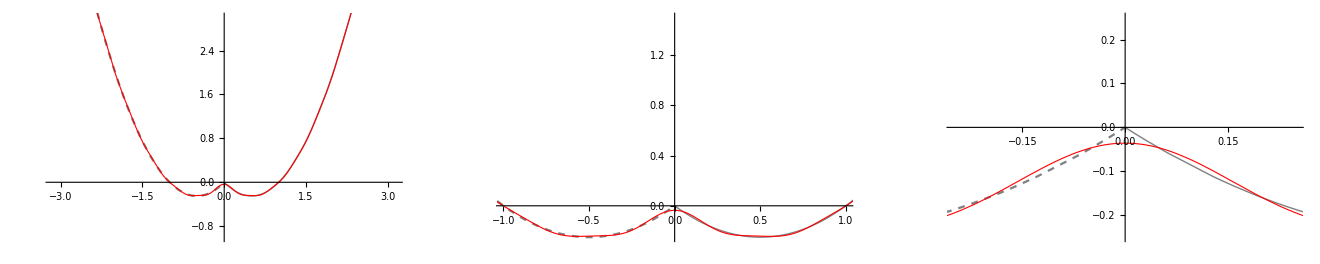

```mathematica
fserCosParts=Array[Take[fserCos,#1]&,nr];
Manipulate[Show[p1,p2,Plot[fserCosParts[[n]],{x,-Pi,Pi},PlotStyle->{Red,Thickness[0.002]}]],{n,1,nr,1}];
GraphicsGrid[{Show[p1,p2,Plot[fserCosParts[[nr]],{x,-Pi,Pi},PlotStyle->{Red,Thickness[0.002]}], PlotRange->{{-#[[1]],#[[1]]},{#[[2]],#[[3]]}}]&/@{{Pi,-1,3},{1,-0.25,1.5},{0.25,-0.25,0.25}}}]
```